## Algebra

```mathematica
Length[a + b + c + a]
```

3

```mathematica
PolynomialGCD[(1 + x) ^ 4, (1 + x) ^ 6, x^2 + 2 x + 1]
```

(1+x)^2

```mathematica
PolynomialLCM[(1 + x) ^ 4, (1 + x) ^ 6, x^2 + 2 * x + 1]
```

(1+x)^6

```mathematica
Denominator[(1 + x) / x]
```

x

```mathematica
Coefficient[3 * x^2 + a * b * x + x * y * z * b + 2 * c * b^2, b]
```

a x+x y z

```mathematica
Collect[(1 + a + x) ^ 4, x]
```

1+4 a+6 a^2+4 a^3+a^4+(4+12 a+12 a^2+4 a^3) x+(6+12 a+6 a^2) x^2+(4+4 a) x^3+x^4

```mathematica
Collect[(1 + a + x) ^ 4, x, Simplify]
```

(1+a)^4+4 (1+a)^3 x+6 (1+a)^2 x^2+4 (1+a) x^3+x^4

```mathematica
TrigExpand[Sin[2 x]]
```

2 Cos[x] Sin[x]

```mathematica
Series[1/2 * (E^x - E ^ -x), {x, 0, 7}]
```

x+x^3/6+x^5/120+x^7/5040+O[x]^8

```mathematica
SeriesCoefficient[Cos[x], {x, 0, n}]
```

Piecewise[{{(ⅈ^n (1+(-1)^n))/(2 n!), n≥0}, {0, True}}]

```mathematica
f =
    If[0 <= x <= 1,
        x
        ,
        2 - x
    ];

FourierSinSeries[f, x, 3]

FourierCosSeries[f, x, 3]
```

((4-2 π+4 Sin[1]) Sin[x])/π+((-2+π+Sin[2]) Sin[2 x])/π+(2 (6-3 π+2 Sin[3]) Sin[3 x])/(9 π)

1/2 (4-2/π-π)+(4 Cos[1] Cos[x])/π+(4 Cos[3] Cos[3 x])/(9 π)-(2 Cos[2 x] Sin[1]^2)/π

```mathematica
LaplaceTransform[t^2 + 6 t - 3, t, s]
```

2/s^3+6/s^2-3/s

```mathematica
Solve[2 x^2 - x - 1 == 0]
```

{{x→-1/2},{x→1}}

```mathematica
FindRoot[4^x + 2 ^ (x + 1) - 3, {x, 0}]
```

{x→0.}

```mathematica
Solve[a x + y == 7 && b x - y == 1, {x, y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

```mathematica
Reduce[x^2 - 3 x + 2 > 0]
```

x<1||x>2

```mathematica
Reduce[(a - 1) (b - 2) == 0, {a, b}, Integers]
```

a==1||b==2

```mathematica
Simplify[RSolve[{a[n] == a[n - 1] + 3 a[n - 2], a[0] == 1, a[1] == 1},
     a[n], n]]
```

{{a[n]→1/26 (-(1/2 (1-√13))^n (-13+√13)+(1/2 (1+√13))^n (13+√13))}}

```mathematica
Integrate[3 Cos[5 x] / E ^ (2 x), {x, -1, 1}]
```

6/29 (5 Cosh[2] Sin[5]+2 Cos[5] Sinh[2])

```mathematica
Assuming[{a > 0, b > 0}, Integrate[Log[x], {x, a, b}]]
```

ConditionalExpression[a-b-a Log[a]+b Log[b], a≠b]

```mathematica
NIntegrate[Sqrt[(Sin[x]) ^ 3 + 1], {x, 0, 1}]
```

1.08268

```mathematica
f =
    If[x >= 0,
        1 / (1 + x)
        ,
        1 / (1 + E^x)
    ];

Integrate[f, {x, -1, 1}]
```

Log[1+ⅇ]

```mathematica
DSolve[y'[x] - 3 x y[x] == 2 x, y[x], x]
```

DSolve::dsfun: 7-5 x^2 不能用作函数.

DSolve[-10 x-3 x (7-5 x^2)==2 x,7-5 x^2,x]

```mathematica
DSolve[{y''[x] + 2 y'[x] + 2 y[x] == -E - x, y[0] == 0, y'[0] == 0}, 
    y[x], x]
```

DSolve::dsfun: 7-5 x^2 不能用作函数.

DSolve[{-10-20 x+2 (7-5 x^2)==-ⅇ-x,False,True},7-5 x^2,x]

## Matrix

```mathematica
{{1, 2}, {3, 4}} // MatrixForm
```

(1 | 2
3 | 4)

## Graphics

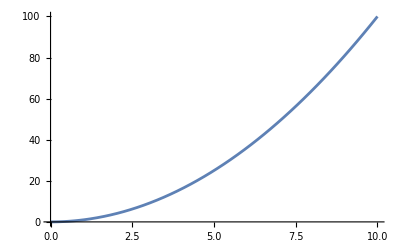

```mathematica
Plot[x^2, {x, 0, 10}]
```

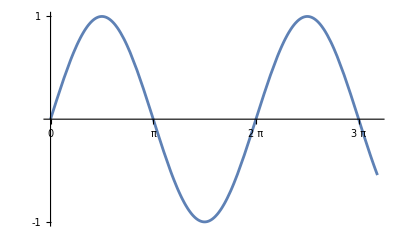

```mathematica
Plot[Sin[x], {x, 0, 10}, Ticks -> {{0, Pi, 2 Pi, 3 Pi}, {-1, 1}}]
```

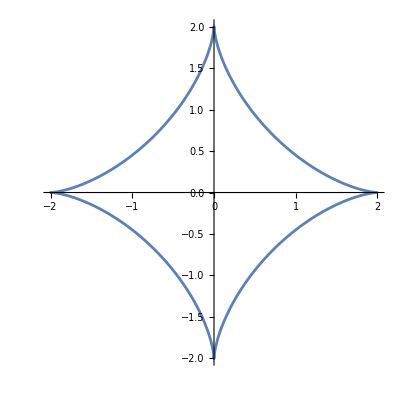

```mathematica
ParametricPlot[{2 (Cos[t]) ^ 3, 2 (Sin[t]) ^ 3}, {t, 0, 2 Pi}]
```

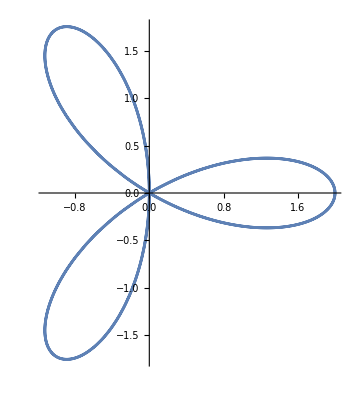

```mathematica
PolarPlot[2 Cos[3 θ], {θ, 0, 2 Pi}]
```

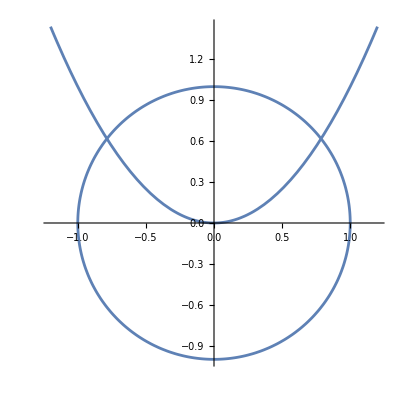

```mathematica
pic1 = Plot[x^2, {x, -1.2, 1.2}];

pic2 = PolarPlot[1, {θ, 0, 2 Pi}];

Show[pic1, pic2, {PlotRange -> All, AspectRatio -> 1}]
```

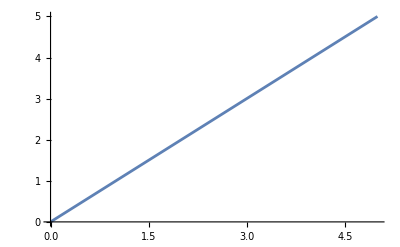

```mathematica
Plot[x, {x, -0, 5}, AxesStyle -> Arrowheads[0.07]]
```

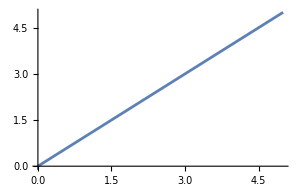

```mathematica
Plot[x, {x, -0, 5}, ImageSize -> 300]
```

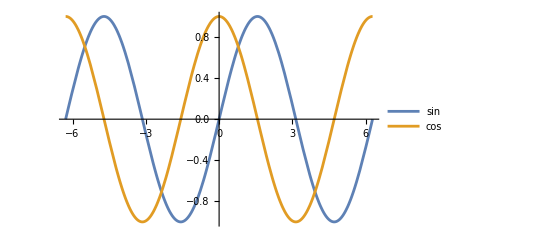

```mathematica
Plot[{Sin[x], Cos[x]}, {x, -2 Pi, 2 Pi}, {PlotLegends -> {sin, cos}}]
```

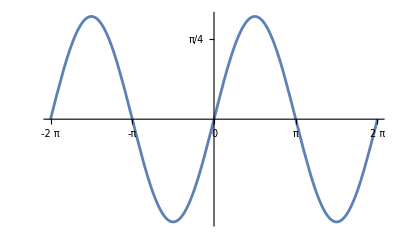

```mathematica
ticks = Table[Pi * i, {i, -2, 2, 1/4}];

pic = Plot[Sin[x], {x, -2 Pi, 2 Pi}, Ticks -> {ticks}, TicksStyle -> 
    20];

Magnify[pic, 0.4]
```

```mathematica
ParametricPlot3D[{Sin[t], Cos[t], t / 5}, {t, -9, 7}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2 + y^2 == z, {x, -2, 2}, {y, -2, 2}, {z, 0, 2}, PlotPoints
     -> 40]
```

-Graphics3D-

## Animated

```mathematica
Animate[Plot3D[5 Sin[2 Pi t - Pi (x + 2 y)], {x, -1, 1}, {y, -1, 1}, 
    PlotPoints -> 30], {t, 0, Infinity}]
```

```mathematica
Animate[ParametricPlot[{Cos[x] - Cos[80 x] Sin[x], 2 Sin[x] - Sin[80 
    x]}, {x, 0, t}, PlotPoints -> 200, PlotRange -> {{-1.5, 1.5}, {-3, 3}
    }], {t, 0, 7}]
```

```mathematica
x[t_] = 7 t;

y[t_] = 7 - 5 t^2;

Animate[Graphics[{Disk[{x[t], y[t]}, 0.1]}, PlotRange -> {{0, 10}, {0,
     9}}], {t, 0, 2}, RefreshRate -> 60]
```